```mathematica
(*Tensor of triangle*)
Tensor=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Tensor[[2,2,2]]=1;
Tensor[[1,1,2]]=-1;
Tensor[[1,2,1]]=-1;
Tensor[[2,1,1]]=-1;
```

```mathematica
(*Get the rotation matrix along z, for positive rotflake, flake rotates anticlockwise*)
(*Get the rotation matrix along -y, for positive tiltflake, flake rotates in xz plane anticlockwise*)
R1[rotflake_]:=Transpose[{{Cos[rotflake],Sin[rotflake],0},{-Sin[rotflake],Cos[rotflake],0},{0,0,1}}]
R2[tiltflake_]:=Transpose[{{Cos[tiltflake],0,Sin[tiltflake]},{0,1,0},{-Sin[tiltflake],0,Cos[tiltflake]}}]
R[rotflake_,tiltflake_]:=R2[tiltflake].R1[rotflake]
```

```mathematica
(*Get the SHG tensor after flake rotation and tilt*)
RotTensor[rotflake_,tiltflake_]:=Table[(R[rotflake,tiltflake][[i,;;]].Tensor[[;;,;;,;;]].Inverse[R[rotflake,tiltflake]][[;;,j]]).Inverse[R[rotflake,tiltflake]][[;;,k]],{i,1,3},{j,1,3},{k,1,3}]
```

```mathematica
(*Get the SHG tensor for nanoscroll, roll direction is determined by rotflake*)
NanoscrollTensor[rotflake_]:=Integrate[RotTensor[rotflake,tiltflake],{tiltflake,0,2Pi}]/(2Pi)//FullSimplify
(*Rotate the Nanoscroll， positive for anticlockwise*)
R3[rotnanoscroll_]:=Transpose[{{Cos[rotnanoscroll],Sin[rotnanoscroll],0},{-Sin[rotnanoscroll],Cos[rotnanoscroll],0},{0,0,1}}]
(*roll and rotate roll*)
RotNanoscrollTensor[rotflake_,rotnanoscroll_]:=Table[(R3[rotnanoscroll][[i,;;]].NanoscrollTensor[rotflake][[;;,;;,;;]].Inverse[R3[rotnanoscroll]][[;;,j]]).Inverse[R3[rotnanoscroll]][[;;,k]],{i,1,3},{j,1,3},{k,1,3}]
```

```mathematica
tensor0=RotNanoscrollTensor[-x,0]//FullSimplify;
```

```mathematica
tensor0//MatrixForm
```

((0
-1/2 Cos[3 x]
0) | (-1/2 Cos[3 x]
0
0) | (0
0
0)
(-1/2 Cos[3 x]
0
0) | (0
Cos[3 x]
0) | (0
0
-1/2 Cos[3 x])
(0
0
0) | (0
0
-1/2 Cos[3 x]) | (0
-1/2 Cos[3 x]
0))

```mathematica
Erot={E0*Cos[theta],E0*Sin[theta],0};
```

```mathematica
{Cos[theta],Sin[theta],0}.(tensor0.Erot.Erot)//FullSimplify//MatrixForm
```

-1/4 E0^2 (1+5 Cos[2 theta]) Cos[3 x] Sin[theta]

```mathematica
in[x_,theta_]:=(-1/4  (1+5 Cos[2 theta]) Cos[3 x] Sin[theta])^2
```

```mathematica
(-1/4  (1+5 Cos[2 theta]) Cos[3 x] Sin[theta])^2/.theta->Pi/2
```

Cos[3 x]^2

```mathematica
a1={1,0};
a2={1/2,√3/2};
angle[m_,n_]:=Module[{vec=m*a1+n*a2,theta},theta=ArcTan[vec[[1]],vec[[2]]];theta]
len[m_,n_]:=Norm[m*a1+n*a2]
nanotube[m_,n_]:=If[And[m==0,n==0],0,Cos[3*angle[m,n]]^2*len[m,n]^2]
```

```mathematica
ans=Flatten[Table[{m+1/2*n,n*√3/2,nanotube[m,n]}//N,{m,-40,40},{n,-40,40}],1];
```

```mathematica
Export[NotebookDirectory[]<>"output1.xlsx",ans]
```

D:\Users\qqk\Desktop\output1.xlsx

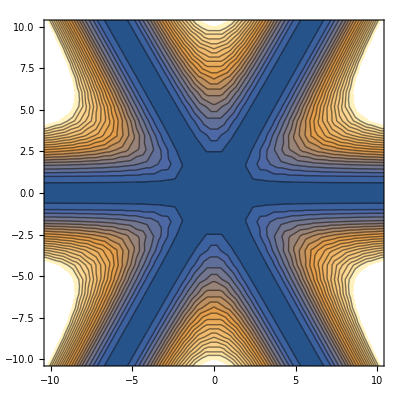

```mathematica
ListContourPlot[ans,PlotRange->{{-10,10},{-10,10},{0,100}},Contours->20]
```

```mathematica
(*From tensor to intensity*)
Intensity[thetain_,tensor_,thetaout_]:=Abs[{Cos[thetaout],Sin[thetaout],0}.tensor.{Cos[thetain],Sin[thetain],0}.{Cos[thetain],Sin[thetain],0}]^2
```

((0.
-0.5
0.) | (-0.5
0.
0.) | (0.
0.
0.)
(-0.5
0.
0.) | (0.
1.
0.) | (0.
0.
-0.5)
(0.
0.
0.) | (0.
0.
-0.5) | (0.
-0.5
0.))

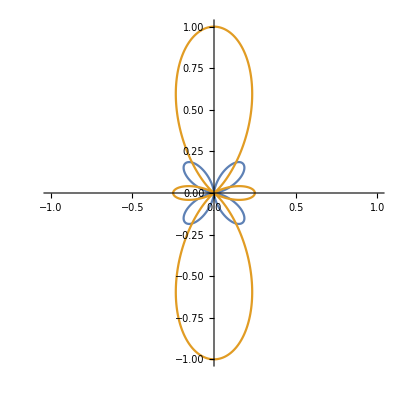

```mathematica
tensor0=RotNanoscrollTensor[0/180*Pi,0/180*Pi]//N;
tensor0//MatrixForm
ans1=Table[{theta,Intensity[theta,tensor0,0]},{theta,0,2Pi,0.01}];
ans2=Table[{theta,Intensity[theta,tensor0,90/180*Pi]},{theta,0,2Pi,0.01}];
ListPolarPlot[{ans1,ans2},Joined->True,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
Export[NotebookDirectory[]<>"output1.xlsx",ans1]
Export[NotebookDirectory[]<>"output2.xlsx",ans2]
```

E:\PSU\My journal paper\#6 SHG of MoS2 Nanoscroll\output1.xlsx

E:\PSU\My journal paper\#6 SHG of MoS2 Nanoscroll\output2.xlsx

```mathematica
tensor0=({{({{xxx}, {xxy}, {xxz}}), ({{xxy}, {xyy}, {xyz}}), ({{xxz}, {xyz}, {xzz}})}, {({{xxy}, {xyy}, {xyz}}), ({{xyy}, {yyy}, {yyz}}), ({{xyz}, {yyz}, {yzz}})}, {({{xxz}, {xyz}, {xzz}}), ({{xyz}, {yyz}, {yzz}}), ({{xzz}, {yzz}, {zzz}})}});
Intensity[theta,tensor0,Pi/2]//FullSimplify
```

Abs[xxy Cos[theta]^2+yyy Sin[theta]^2+xyy Sin[2 theta]]^2

```mathematica
(xxx -xyy)Cos[theta]^2+xyy +xxy Sin[2 theta]
```

```mathematica
(xxx -xyy)(Cos[2theta]+1)/2+xyy +xxy Sin[2 theta]
```

```mathematica
(xxx +xyy)/2 +xxy Sin[2 theta]+(xxx -xyy)/2 Cos[2theta]
```

```mathematica
(yyy+xxy)/2+xyy Sin[2 theta]+(xxy-yyy)/2 Cos[2theta]
```

```mathematica
Animate[PolarPlot[A +Cos[2theta],{theta,0,2Pi}],{A,-3,3}]
```

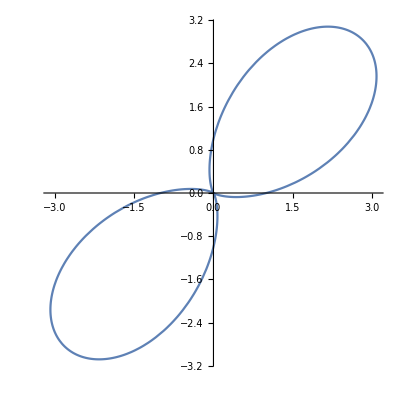

```mathematica
PolarPlot[(1+Sin[2x])^2,{x,0,2Pi}]
```